```mathematica
(* ==========================0. Pre-optimization: Clean up environment==========================*)Quiet[CloseKernels[]];

(* ==========================1. Global Fundamental Constants==========================*)
YearInS=31536000.;
MsunInS=4.92*10^(-6);
AuInS=499.0;
PcInS=1.029*10^8;
SmbhInSun=4*10^6;
M3InS=SmbhInSun*MsunInS;
Eoval=0.9;
AoInM3=2500;
AoInS=AoInM3*M3InS;
M1Sun=1.4;
M2Sun=1.4;
M1InS=M1Sun*MsunInS;
M2InS=M2Sun*MsunInS;
Iota3Val=0;
Omega3Val=0;
PoInS=(4 Pi^2*AoInS^3/(M3InS))^0.5;
TobsInS=4.0*YearInS;
DlInS=8.0*10^3*PcInS;
AiMin=0.007;

(* ==========================2. Compiled High-Frequency Functions==========================*)
ARInAuComp=Compile[{{ei,_Real}},AoInS*((M1InS+M2InS)/(3*M3InS))^(1/3)*(1-Eoval)/((1+ei)*AuInS),RuntimeAttributes->{Listable}];
ARInAu[ei_]:=ARInAuComp[ei];
AiMaxSample=ARInAu[0];

EiFromAiKozaiComp=Compile[{{ai,_Real}},Sqrt[1-(AoInS/ai/AuInS)^2*(1-Eoval^2)/34^2*(ai*AuInS/(PcInS/100))^(-2/3)*((M1InS+M2InS)/(2*10^6*MsunInS))^(2/3)*(2*M3InS/(M1InS+M2InS))^(-2/3)]];
EiFromAiKozai[ai_]:=EiFromAiKozaiComp[ai];

GneComp=Compile[{{n,_Integer},{e,_Real}},Module[{besselNm2,besselNm1,besselN,besselNp1,besselNp2,term1,term2,term3},besselNm2=BesselJ[n-2,n e];
besselNm1=BesselJ[n-1,n e];
besselN=BesselJ[n,n e];
besselNp1=BesselJ[n+1,n e];
besselNp2=BesselJ[n+2,n e];
term1=(besselNm2-2 e besselNm1+(2/n) besselN+2 e besselNp1-besselNp2)^2;
term2=(1-e^2) (besselNm2-2 besselN+besselNp2)^2;
term3=(4/(3 n^2)) besselN^2;
(n^4/32) (term1+term2+term3)],RuntimeAttributes->{Listable}];
Gne[n_,e_]:=GneComp[n,e];

(* ==========================3. ZLK Evolution Equations==========================*)
DeToDtau[m1_,m2_,α_,e_,ι_,Ω_,ω_,m3_,A_,Eo_,ι3_,Ω3_]:=(15 π α^3 e Sqrt[1-e^2] m3)/(16 A^3 (1-Eo^2)^(3/2) (m1+m2))*(Sin[ι3]^2 (Cos[2 ι]+3) Sin[2 ω] Cos[2 Ω-2 Ω3]+4 Sin[ι3]^2 Cos[ι] Cos[2 ω] Sin[2 Ω-2 Ω3]-4 Sin[2 ι3] Sin[ι] Cos[2 ω] Sin[Ω-Ω3]-2 Sin[2 ι] Sin[2 ι3] Sin[2 ω] Cos[Ω-Ω3]+Sin[ι]^2 (3 Cos[2 ι3]+1) Sin[2 ω]);
DIotaToDtau[m1_,m2_,α_,e_,ι_,Ω_,ω_,m3_,A_,Eo_,ι3_,Ω3_]:=(3 π α^3 m3)/(4 A^3 Sqrt[1-e^2] (1-Eo^2)^(3/2) (m1+m2))*(Sin[ι] Sin[ι3] Cos[Ω-Ω3]+Cos[ι] Cos[ι3])*(Sin[ι3] Sin[Ω-Ω3] (5 e^2 Cos[2 ω]+3 e^2+2)+5 e^2 Sin[2 ω] (Sin[ι3] Cos[ι] Cos[Ω-Ω3]-Sin[ι] Cos[ι3]));
DOmegaToDtau[m1_,m2_,α_,e_,ι_,Ω_,ω_,m3_,A_,Eo_,ι3_,Ω3_]:=(3 π α^3 m3)/(4 A^3 Sqrt[1-e^2] (1-Eo^2)^(3/2) (m1+m2))*(Sin[ι3] Cos[Ω-Ω3]+Cos[ι3] Cot[ι])*(5 e^2 Sin[ι3] Sin[2 ω] Sin[Ω-Ω3]+(5 e^2 Cos[2 ω]-3 e^2-2) (Sin[ι] Cos[ι3]-Sin[ι3] Cos[ι] Cos[Ω-Ω3]));
DOmegaBarToDtau[m1_,m2_,α_,e_,ι_,Ω_,ω_,m3_,A_,Eo_,ι3_,Ω3_]:=(3 π α^3 Sqrt[1-e^2] m3)/(8 A^3 (1-Eo^2)^(3/2) (m1+m2))*(10 Sin[ι] Sin[2 ι3] Sin[2 ω] Sin[Ω-Ω3]+Sin[ι3]^2 Cos[2 Ω-2 Ω3] (2 Sin[ι]^2 (4-5 Cos[ω]^2)+20 Cos[ω]^2-10)-10 Sin[ι3]^2 Cos[ι] Sin[2 ω] Sin[2 Ω-2 Ω3]+Sin[2 ι] Sin[2 ι3] (3-5 Cos[2 ω]) Cos[Ω-Ω3]+(3 Cos[2 ι3]+1) (Sin[ι]^2 (5 Cos[ω]^2-4)+1));
DOmegaToDtau2[m1_,m2_,α_,e_,ι_,Ω_,ω_,m3_,A_,Eo_,ι3_,Ω3_]:=DOmegaBarToDtau[m1,m2,α,e,ι,Ω,ω,m3,A,Eo,ι3,Ω3]-DOmegaToDtau[m1,m2,α,e,ι,Ω,ω,m3,A,Eo,ι3,Ω3]*Cos[ι];

Eqns={eSecular'[τ]==DeToDtau[m1,m2,α,eSecular[τ],ιSecular[τ],ΩSecular[τ],ωSecular[τ],m3,A,Eo,ι3,Ω3],ιSecular'[τ]==DIotaToDtau[m1,m2,α,eSecular[τ],ιSecular[τ],ΩSecular[τ],ωSecular[τ],m3,A,Eo,ι3,Ω3],ΩSecular'[τ]==DOmegaToDtau[m1,m2,α,eSecular[τ],ιSecular[τ],ΩSecular[τ],ωSecular[τ],m3,A,Eo,ι3,Ω3],ωSecular'[τ]==DOmegaToDtau2[m1,m2,α,eSecular[τ],ιSecular[τ],ΩSecular[τ],ωSecular[τ],m3,A,Eo,ι3,Ω3]};

(* ==========================4. LISA Noise & SNR Basic Functions==========================*)
Poms=(1.5*10^(-11))^2;
Pacc[f_]=(3*10^(-15))^2*(1+(0.4/10^3/f)^2);
Llisa=2.5*10^9;
FstarLisa=19.09/10^3;
Pn[f_]:=Poms/Llisa^2+4 Pacc[f]/((2 π f)^4*Llisa^2);
R[f_]:=3/10/(1+0.6*(f/FstarLisa)^2);
AlphaFitpara=0.138;BetaFitpara=-221;KappaFitpara=521;GammaFitpara=1680;FkFitpara=0.00113;AFitpara=9*10^(-45);
Sc[f_]:=AFitpara*f^(-7/3)*E^(-f^AlphaFitpara+BetaFitpara*f*Sin[KappaFitpara*f])*(1+Tanh[GammaFitpara*(FkFitpara-f)]);
SnLisa[f_]:=Pn[f]/R[f]+Sc[f];

H0[m1_,m2_,α_,Dl_]:=Sqrt[32/5]*(m1*m2)/(Dl*α);
NmaxOfE[ei_]:=Floor[(5 (1+ei)^0.5)/(1-ei)^1.5];
Fiorb[m1_,m2_,α_]:=Sqrt[(m1+m2)/α^3]/(2 π);

(* ==========================5. Solve Zlk: Robust Return==========================*)
SolveZlk[ai_,ei_,ι_,Ω_,ω_]:=Module[{aiInS,piorbInS,tauMax,ics,parameters,solResult},aiInS=ai*AuInS;
piorbInS=(4 Pi^2*aiInS^3/(M1InS+M2InS))^0.5;
tauMax=4*YearInS/piorbInS; (*4yr observation time*)
ics={eSecular[0]==ei,ιSecular[0]==ι,ΩSecular[0]==Ω,ωSecular[0]==ω};
parameters={m1->M1InS,m2->M2InS,m3->M3InS,α->aiInS,A->AoInS,Eo->Eoval,ι3->Iota3Val,Ω3->Omega3Val};
solResult=Quiet[NDSolve[Join[Eqns,ics]/. parameters,{eSecular,ιSecular,ΩSecular,ωSecular},{τ,0,tauMax},Method->"LSODA",MaxSteps->10^5,AccuracyGoal->8,PrecisionGoal->8,WorkingPrecision->12],{NDSolve::ndsz,NDSolve::ndcf,NDSolve::mxst,General::munfl,General::unfl,(* ←underflow:e->1*)Power::infy,Infinity::indet}];
If[MatchQ[solResult,{{__Rule}}],{First[solResult],piorbInS},{$Failed,0}]];

(* ==========================6. Calculate SnrZlkFromSol==========================*)
CalculateSnrZlkFromSol[ai_,sol_,piorbInS_]:=Module[{aiInS,nDeccfunc,nIotaFunc,dt,tValues,eValues,iotaValues,eThreshold,firstOverPos,h0Val,f,const,maxNmax,nlist,freqs,denomlist,results,beforeLen,afterLen,resultsBefore,singleAfterResult,baseSnr,inclinationFactorBefore,singleInclinationFactorAfter},aiInS=ai*AuInS;
nDeccfunc[t_]=eSecular[t/piorbInS]/. sol;
nIotaFunc[t_]=ιSecular[t/piorbInS]/. sol;
dt=TobsInS/20;
tValues=Range[dt/2,TobsInS-dt/2,dt];
eValues=nDeccfunc/@tValues;
(*生成20个分段的倾角值，每段内看作不变*)iotaValues=nIotaFunc/@tValues;
(*Apply zlk dominated*)eThreshold=EiFromAiKozai[ai];
If[!NumericQ[eThreshold],Return[Indeterminate]];
firstOverPos=FirstPosition[eValues,e_/;e>eThreshold,Missing["NotFound"]];
If[firstOverPos=!=Missing["NotFound"],eValues[[firstOverPos[[1]];;]]=eThreshold;];
h0Val=H0[M1InS,M2InS,aiInS,DlInS];
f=Fiorb[M1InS,M2InS,aiInS];
const=(8/Sqrt[5])*h0Val*Sqrt[0.885895*dt];
maxNmax=Max[NmaxOfE/@eValues];
maxNmax=Min[maxNmax,2500];(*最多算到2500次谐波*)nlist=Range[maxNmax];
freqs=nlist*f;
denomlist=1./(nlist^2*SnLisa[freqs]);
(*拆分恒定偏心率片段，仅计算1次避免重复*)beforeLen=If[firstOverPos===Missing["NotFound"],Length[eValues],firstOverPos[[1]]-1];
afterLen=Length[eValues]-beforeLen;
(*计算前半段：偏心率和倾角均逐段变化，每段内看作不变*)resultsBefore=Table[Module[{currentE,currentIota,currentNmax,sumTerm,snrSegment},currentE=eValues[[i]];
currentIota=iotaValues[[i]];currentNmax=Min[NmaxOfE[currentE],2500];
sumTerm=Sum[Gne[n,currentE]*denomlist[[n]],{n,1,currentNmax}];
snrSegment=const*Sqrt[sumTerm];
(*当前段的倾角因子，先不乘，后面统一平方和*){snrSegment,currentIota}],{i,beforeLen}];
(*后半段：偏心率和倾角恒定*)singleAfterResult=0;
singleInclinationFactorAfter=1;
If[afterLen>0,Module[{currentE=eThreshold,currentIota,currentNmax,sumTerm},(*后半段倾角取阈值跨越时刻的对应值，这里统一取firstOverPos对应的值*)currentIota=If[firstOverPos=!=Missing["NotFound"],iotaValues[[firstOverPos[[1]]]],iotaValues[[-1]]];
currentNmax=Min[NmaxOfE[currentE],2500];
sumTerm=Sum[Gne[n,currentE]*denomlist[[n]],{n,1,currentNmax}];
singleAfterResult=const*Sqrt[sumTerm];
singleInclinationFactorAfter=Sqrt[(Cos[currentIota]^2+(1+Cos[currentIota]^2)^2/4)*1.25];]];
(*总信噪比：前半段逐段计算倾角因子，平方和+后半段单次贡献平方×片段数*)baseSnr=Sqrt[Total[Table[(resultsBefore[[i,1]]*Sqrt[(Cos[resultsBefore[[i,2]]]^2+(1+Cos[resultsBefore[[i,2]]]^2)^2/4)*1.25])^2,{i,beforeLen}]]+afterLen*(singleAfterResult*singleInclinationFactorAfter)^2];
baseSnr];

(* ==========================7. Helper Function InRegion2==========================*)
signalToNoise[m1_,m2_,α_,e_,Dl_,Tobs_,ci_]:=Module[{h0Val,f,nlist,nmax,freqs,denomlist,const,sumTerm},(*1. Get amplitude and orbital frequency (match your defined functions)*)h0Val=H0[m1,m2,α,Dl];
f=Fiorb[m1,m2,α];
(*2. Calculate maximum harmonic number (vectorized compiled function)*)nmax=Min[NmaxOfE[e],2500];
nlist=Range[1,nmax];
(*3. Vectorized calculation:harmonic frequencies and noise denominator*)freqs=nlist*f;
denomlist=1/(nlist^2*SnLisa[freqs]);
(*4. Precompute constant coefficient*)const=(8/Sqrt[5])*h0Val*Sqrt[0.885895*Tobs];
sumTerm=Sum[Gne[n,e]*denomlist[[n]],{n,1,nmax}];
const*Sqrt[sumTerm]*Sqrt[(ci^2+(1+ci^2)^2/4)*1.25]];

InRegion2[ai_,ei_,ci_]:=Module[{snr},If[ai<AiMin||ai>ARInAu[ei],Return[False]];
snr=signalToNoise[M1InS,M2InS,ai*AuInS,ei,DlInS,TobsInS,ci];
NumericQ[snr]&&snr>=5];

(* ==========================8. Launch Parallel Kernels==========================*)
LaunchKernels[18];

(* ==========================9. Core Logic: CalculateRegionCounts==========================*)
CalculateRegionCounts[eiRandom_List,XRandom_List,IotaRandom_List,OmegaRandom_List,PericenterRandom_List]:=Module[{pointsInRegion2,candidateMask,candidateIndices,candidateData,resultsParallel,pointsInRegion1,areaRatio,region1Points,region2Points,region2Mask,aRVec,eThresholdVec},(* ==========================Region2:Pure Algebraic Criterion==========================*)region2Mask=MapThread[InRegion2[#1,#2,Cos[#3]]&,{XRandom,eiRandom,IotaRandom}];
pointsInRegion2=Total@Boole@region2Mask;
(*Collect Region2 scatter points {ai,1-ei} for plotting*)region2Points=If[Length[region2Mask]===0||!MemberQ[region2Mask,True],{},Pick[Transpose@{XRandom,1-eiRandom},region2Mask,True]];
(* ==========================Vectorized Pre-filtering for Region1==========================*)(*Vectorize ARInAu and EiFromAiKozai over the full sample at once,avoiding repeated single-point calls inside MapThread*)aRVec=ARInAu/@eiRandom;(*tidal radius for each ei*)eThresholdVec=EiFromAiKozai/@XRandom;(*Kozai threshold for each ai*)(*Build candidate mask using vectorized comparisons*)candidateMask=MapThread[Function[{ai,ei,aR,eThreshold},If[ai<AiMin||ai>aR,False,If[!NumericQ[eThreshold],False,ei<=eThreshold]]],{XRandom,eiRandom,aRVec,eThresholdVec}];
candidateIndices=Flatten@Position[candidateMask,True];
(* ==========================Pack Candidate Data into Tuples==========================*)If[Length[candidateIndices]===0,(*No candidates:return zeros immediately*)Return[{0,pointsInRegion2,If[pointsInRegion2==0,Missing["Undefined"],N[0/pointsInRegion2]],{},region2Points}]];
(* ==========================Pack Candidate Data (only orbital elements)==========================*)candidateData=Transpose@{XRandom[[candidateIndices]],eiRandom[[candidateIndices]],IotaRandom[[candidateIndices]],OmegaRandom[[candidateIndices]],PericenterRandom[[candidateIndices]]};
(* ==========================Evaluate Each Candidate (Direct ODE+SNR)==========================*)resultsParallel=ParallelMap[Function[data,Module[{aiVal,eiVal,ιVal,ΩVal,ωVal,sol,piorbInS,snrZlk},(*Unpack tuple:only orbital elements*){aiVal,eiVal,ιVal,ΩVal,ωVal}=data;
(*Directly solve ODE and calculate SNR for all candidates*){sol,piorbInS}=Quiet@SolveZlk[aiVal,eiVal,ιVal,ΩVal,ωVal];
If[sol===$Failed,False,If[!MatchQ[sol,{eSecular->_InterpolatingFunction,ιSecular->_InterpolatingFunction,ΩSecular->_InterpolatingFunction,ωSecular->_InterpolatingFunction}],False,snrZlk=Quiet@Check[CalculateSnrZlkFromSol[aiVal,sol,piorbInS],Indeterminate];
NumericQ[snrZlk]&&snrZlk>=5]]]],candidateData];
(*Sanitize any unevaluated Return artifacts*)resultsParallel=resultsParallel/. {Null->False};
pointsInRegion1=Total@Boole[resultsParallel];
(* ==========================Collect Region1 Scatter Points for Plotting==========================*)region1Points=If[!MemberQ[resultsParallel,True],{},Module[{passing},passing=Pick[candidateData,resultsParallel,True];
{#[[1]],1-#[[2]]}&/@passing   (*{ai,1-ei}*)]];
(* ==========================Area Ratio==========================*)areaRatio=If[pointsInRegion2==0,Missing["Undefined"],N[pointsInRegion1/pointsInRegion2]];
(*Return:counts+scatter point lists for plotting*){pointsInRegion1,pointsInRegion2,areaRatio,region1Points,region2Points}];

(* ==========================10. Generate All Sampling Data==========================*)
NPoints=10^5;
SeedRandom[125];

(*Generate common semi-major axis and angle samples*)
XRandom=(RandomReal[{0,1},NPoints]*(AiMaxSample^5-AiMin^5)+AiMin^5)^(1/5);
CosIotaRandom=RandomReal[{-1,1},NPoints];
IotaRandom=ArcCos[CosIotaRandom];
OmegaRandom=RandomReal[{0,2 Pi},NPoints];
PericenterRandom=RandomReal[{0,2 Pi},NPoints];

(*Generate eccentricity samples for both distributions*)
YMin=0;YMax=1;
Con=(1-YMin)^2-(1-YMax)^2;
U=RandomReal[{0,1},NPoints];
Term=(1-YMin)^2-U*Con;
YRandomThermal=1-Sqrt[Term];
EiRandomThermal=1-YRandomThermal;

YRandomUniform=RandomReal[{0,1},NPoints];
EiRandomUniform=1-YRandomUniform;

(* ==========================Part 1: Thermal y Distribution==========================*)
Print["\n===== [Part 1: Thermal y Distribution Results] ====="];

{timeThermal,{pointsInRegion1Thermal,pointsInRegion2Thermal,areaRatioThermal,region1PointsThermal,region2PointsThermal}}=AbsoluteTiming[CalculateRegionCounts[EiRandomThermal,XRandom,IotaRandom,OmegaRandom,PericenterRandom]];

(*Convert seconds to hours and minutes*)
hoursThermal=timeThermal/3600;
minutesThermal=timeThermal/60;
Print["Computation Time: ",NumberForm[hoursThermal,{3,2}]," hr (== ",NumberForm[minutesThermal,{4,1}]," min)"];
Print["Points in Region 1: ",pointsInRegion1Thermal];
Print["Points in Region 2: ",pointsInRegion2Thermal];
Print["Region 1 / Region 2 Ratio: ",areaRatioThermal];
```

===== [Part 1: Thermal y Distribution Results] =====

Computation Time: 4.70 hr (== 282.0 min)

Points in Region 1: 2266

Points in Region 2: 409

Region 1 / Region 2 Ratio: 5.54034

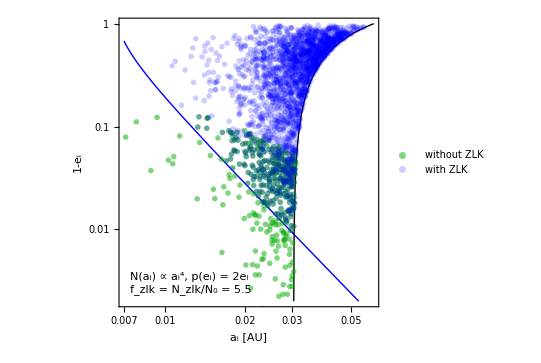

```mathematica
(* ==========================Shared Point Styles==========================*)styleRegion1=Directive[Blue,PointSize[0.01],Opacity[0.2],EdgeForm[{White,Thickness[0.001]}]];
styleRegion2=Directive[Darker@Green,PointSize[0.01],Opacity[0.5],EdgeForm[{Green,Thickness[0.003]}]];

(* ==========================Safe Point List Helper==========================*)
(*Replace empty list with an out-of-range dummy point to avoid ListLogLogPlot::lpn error when no points satisfy the criterion*)
safePoints[pts_List]:=If[Length[pts]===0,{{-9999,-9999}},pts];

(*Roche limit*)
EiFromAR[ai_]:=Abs[1-AoInS/AuInS/ai*((M1InS+M2InS)/(3*M3InS))^(1/3)*(1-Eoval)];

curvePlot=LogLogPlot[{1-EiFromAiKozai[ai],1-EiFromAR[ai]},{ai,AiMin,AiMaxSample},PlotStyle->{{Blue,Thick},{Black,Thick}},PlotRange->{{AiMin,AiMaxSample},{0.002,YMax}},Frame->True,FrameLabel->{{Style[Row[{"1-",Subscript[Style["e",Italic],Style["i",FontSlant->"Plain"]]}],Black,20,FontFamily->"Times New Roman"],None},{Style[Row[{Subscript[Style["a",Italic],Style["i",FontSlant->"Plain"]]," [AU]"}],Black,18,FontFamily->"Times New Roman"],None}},FrameTicks->Automatic,FrameStyle->Directive[Black,14],AspectRatio->1/1.1,PlotPoints->10,ImageSize->400];

(* ==========================Thermal Distribution Plot==========================*)

(*Scatter points for thermal distribution*)
scatterThermal=ListLogLogPlot[{safePoints[region2PointsThermal],safePoints[region1PointsThermal]},PlotStyle->{styleRegion2,styleRegion1},PlotRange->{{AiMin,AiMaxSample},{YMin,YMax}},PlotLegends->Placed[Map[Style[#,FontFamily->"Times New Roman",FontSize->14]&,{"without ZLK","with ZLK"}],Scaled[{0.16,0.24}]]];

(*Annotation:distribution label+f_zlk ratio,placed at lower-left*)
epilogThermal={Text[Column[{(*第一行：N,a,p,e 设为斜体，下标 i 保持正体*)Style[Row[{Style["N",Italic,FontFamily->"Times New Roman"],"(",Subscript[Style["a",Italic,FontFamily->"Times New Roman"],Style["i",Plain,FontFamily->"Times New Roman"]],")"," ∝ ",Subscript[Style["a",Italic,FontFamily->"Times New Roman"],Style["i",Plain,FontFamily->"Times New Roman"]]^4,", ",Style["p",Italic,FontFamily->"Times New Roman"],"(",Subscript[Style["e",Italic,FontFamily->"Times New Roman"],Style["i",Plain,FontFamily->"Times New Roman"]],") = 2",Subscript[Style["e",Italic,FontFamily->"Times New Roman"],Style["i",Plain,FontFamily->"Times New Roman"]]}],FontFamily->"Times New Roman",Black,FontSize->15],(*第二行：f,N 设为斜体，下标 zlk/0 保持正体*)Style[Row[{Subscript[Style["f",Italic,FontFamily->"Times New Roman"],Style["zlk",Plain,FontFamily->"Times New Roman"]]," = ",Subscript[Style["N",Italic,FontFamily->"Times New Roman"],Style["zlk",Plain,FontFamily->"Times New Roman"]],"/",Subscript[Style["N",Italic,FontFamily->"Times New Roman"],Style["0",Plain,FontFamily->"Times New Roman"]]," = ",ToString[NumberForm[areaRatioThermal,{2,1}]]}],FontFamily->"Times New Roman",Black,FontSize->15]},Alignment->Left,Spacings->0.8],{Log[0.0074],Log[0.0023]},{-1,-1},BaseStyle->{FontFamily->"Times New Roman"}]};

finalPlotThermal=Show[curvePlot,scatterThermal,Epilog->epilogThermal,ImageSize->400]
```

```mathematica
(* ==========================Export Combined Plot as EPS==========================*)
targetFolder="Three body";
If[SameQ[$OperatingSystem,"Windows"],basePath=FileNameJoin[{$HomeDirectory,"Desktop",targetFolder}]<>"\\",basePath=FileNameJoin[{$HomeDirectory,"Desktop",targetFolder}]<>"/"];
(*Define export file path*)
exportPath=FileNameJoin[{basePath,"RegionCountsThermal.eps"}];
Export[exportPath,finalPlotThermal,"EPS",ImageResolution->500]
```

/Users/fengwenfan/Desktop/Three body/RegionCountsThermal.eps

```mathematica
(* ==========================Part 2: Uniform y Distribution==========================*)Print["===== [Part 2: Uniform y Distribution Results] ====="];

{timeUniform,{pointsInRegion1Uniform,pointsInRegion2Uniform,areaRatioUniform,region1PointsUniform,region2PointsUniform}}=AbsoluteTiming[CalculateRegionCounts[EiRandomUniform,XRandom,IotaRandom,OmegaRandom,PericenterRandom]];

(*Convert seconds to hours and minutes*)
hoursUniform=timeUniform/3600;
minutesUniform=timeUniform/60;
Print["Computation Time: ",NumberForm[hoursUniform,{3,2}]," hr (== ",NumberForm[minutesUniform,{4,1}]," min)"];
Print["Points in Region 1: ",pointsInRegion1Uniform];
Print["Points in Region 2: ",pointsInRegion2Uniform];
Print["Region 1 / Region 2 Ratio: ",areaRatioUniform];

(* ==========================Total Computation Time==========================*)
totalTimeSec=timeUniform+timeThermal;
totalHours=totalTimeSec/3600;
totalMinutes=totalTimeSec/60;
Print["\n===== [Total Computation Time] ====="];
Print["Total: ",NumberForm[totalHours,{3,2}]," hr (== ",NumberForm[totalMinutes,{4,1}]," min)"];

(*Close parallel kernels*)
CloseKernels[];
```

===== [Part 2: Uniform y Distribution Results] =====

Computation Time: 5.26 hr (== 315.8 min)

Points in Region 1: 2520

Points in Region 2: 206

Region 1 / Region 2 Ratio: 12.233

===== [Total Computation Time] =====

Total: 9.96 hr (== 597.8 min)

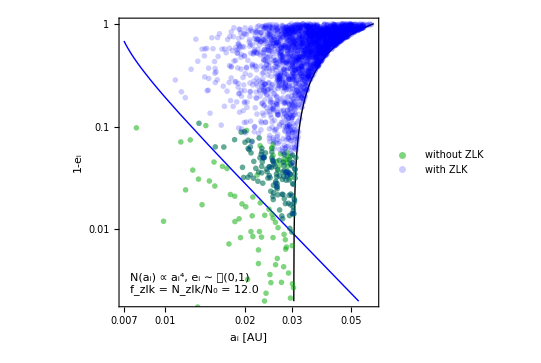

```mathematica
(* ==========================Uniform Distribution Plot==========================*)

(*Scatter points for uniform distribution*)
scatterUniform=ListLogLogPlot[{safePoints[region2PointsUniform],safePoints[region1PointsUniform]},PlotStyle->{styleRegion2,styleRegion1},PlotRange->{{AiMin,AiMaxSample},{YMin,YMax}},PlotLegends->Placed[Map[Style[#,FontFamily->"Times New Roman",FontSize->14]&,{"without ZLK","with ZLK"}],Scaled[{0.16,0.24}]]];

(*Annotation:distribution label+f_zlk ratio,placed at lower-left*)
epilogUniform={Text[Column[{(*第一行：N,a,e 设为斜体*)Style[Row[{Style["N",Italic,FontFamily->"Times New Roman"],"(",Subscript[Style["a",Italic,FontFamily->"Times New Roman"],Style["i",Plain,FontFamily->"Times New Roman"]],")"," ∝ ",Subscript[Style["a",Italic,FontFamily->"Times New Roman"],Style["i",Plain,FontFamily->"Times New Roman"]]^4,", ",Subscript[Style["e",Italic,FontFamily->"Times New Roman"],Style["i",Plain,FontFamily->"Times New Roman"]]," ∼ ",Style["𝓊",FontFamily->"Times New Roman"],"(0,1)"}],FontFamily->"Times New Roman",Black,FontSize->15],(*第二行：f,N 设为斜体，zlk/0保持正体*)Style[Row[{Subscript[Style["f",Italic,FontFamily->"Times New Roman"],Style["zlk",Plain,FontFamily->"Times New Roman"]]," = ",Subscript[Style["N",Italic,FontFamily->"Times New Roman"],Style["zlk",Plain,FontFamily->"Times New Roman"]],"/",Subscript[Style["N",Italic,FontFamily->"Times New Roman"],Style["0",Plain,FontFamily->"Times New Roman"]]," = ",ToString[NumberForm[areaRatioUniform,{2,1}]]}],FontFamily->"Times New Roman",Black,FontSize->15]},Alignment->Left,Spacings->0.8],{Log[0.0074],Log[0.0023]},{-1,-1},BaseStyle->{FontFamily->"Times New Roman"}]};

finalPlotUniform=Show[curvePlot,scatterUniform,Epilog->epilogUniform,ImageSize->400]
```

```mathematica
(*Define export file path*)
exportPath=FileNameJoin[{basePath,"RegionCountsUniform.eps"}];
Export[exportPath,finalPlotUniform,"EPS",ImageResolution->500]
```

/Users/fengwenfan/Desktop/Three body/RegionCountsUniform.eps